See 
http://en.wikipedia.org/wiki/Joseph_Kittinger
http://en.wikipedia.org/wiki/Project_Excelsior
http://hypertextbook.com/facts/JianHuang.shtml

Velocity of a falling object is determined by 

v(t) = (m*g/k)(1-e^(-kt/m))

where g is the acceleration due to gravity, and k is a constant, m is the mass of the object.

```mathematica
m=250;
g=10.;
Solve[m*g/K==274,K]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{K→9.12409}}

274.123 (1-ⅇ^(-0.03648 t))

274.123 (1-0.7^t)

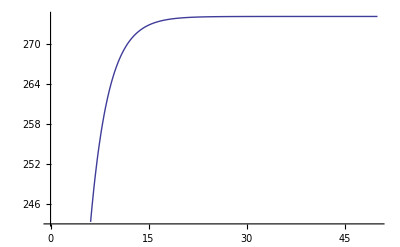

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-5.94129},{t→17.39}}

0.964177

```mathematica
k=9.12;
v[t_]=m*g/k(1-E^(-k*t/m))
v[t_]=m*g/k(1-.7^(t))
Plot[v[t],{t,0,50}]

p[t_]=Integrate[v[x],{x,0,t}];
Solve[p[t]==4000,t]
E^(-k/m)
```

After 4000 meters, a terminal velocity was attained....

```mathematica
v[17.39]
```

273.568